```mathematica
g[x_,b_,c_]:=Piecewise[{{x+1,1<x<3},{x^2+b x+c,Abs[x-2]>=1}}]
Manipulate[Plot[g[x,b,c],{x,-5,5},PlotRange->{{-5,5},{-10,10}}],{b,-5,5},{c,-5,5}]
Limit[f[x],x->2,Direction->1];
Limit[f[x],x->0,Direction->-1];
Limit[f[x],x->4,Direction->1];
Limit[f[x],x->2,Direction->-1];
Solve [9+3 x+y==4&& 1+x+y==2, {x,y}];
```

```mathematica
(* a)Es una discontinuidad que se puede evitar para ciertos valores de "b" y "c" en los que los limites por ambos lados para x=1 y x=3 coinciden,
b.1) f(x)= x^2 cuando -1<x<3, y f(x)=x+5 cuando |x-1|>=2 los puntos donde hay discontinuidad son en x=-1 y x=3,
b.2) f(x)=-(x+3)^2 cuando -4<x<2, y f(x)=x^3 cuando |x+1|>=3 los puntos donde hay discontinuidad son en x=2 y x=-4,
b.3)f(x)=x^3 cuando -8<x<2, y f(x)=7x+2 cuando |x+3|>=5 los puntos donde hay discontinuidad son en x=-8 y x=2,
b.4)f(x)=-8+3 cuando -2<x<8, y f(x)=x^5 cuando |x-3|>=5 los puntos donde hay discontinuidad son en x=-2 y x=8,
b.5)f(x)=x^3 cuando -17/2<x<11/2, y f(x)=-5x+3/4 cuando |x+(3/2)|>=7 los puntos donde hay discontinuidad son en x=-17/2 y x=11/2,
c)segun la ventana, se ve que la funcion se hace continua cuando b=-3 aproximadamente y c=4 aproximadamente,
d)x+1 es fija, la evaluo en 1 y en 3, lo que me da y=2 y y=4 respectivamente, igualo x^2+bx+c a 2 y 4 tomando en cuenta a x=1 y x=3 respectivamente, me queda 1+b+c=2 y 9+3b+c=4, luego hago un sistema de ecuaciones y resulta b=-3 y c=4.

*)
```

```mathematica
2)
```

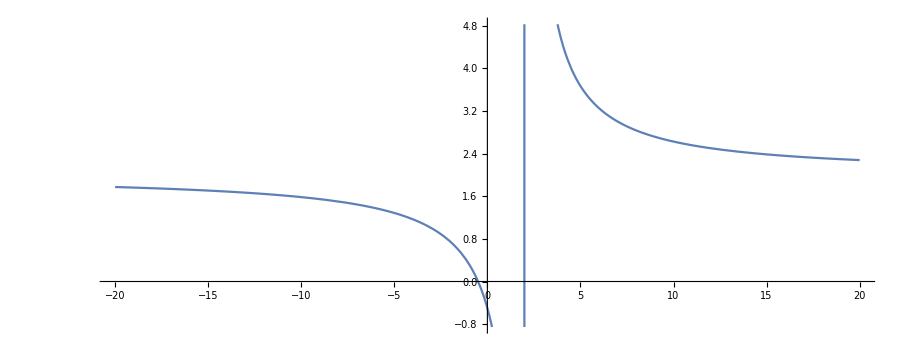

```mathematica
f0[x_]:=Expand[(2x+1)/(x-2)]
Plot[f0[x],{x,-20,20},AspectRatio->Automatic]
```

```mathematica
(*El dominio son todos los numeros reales excepto el 2, la asintota horizontal es en y=2 y la asintota vertical es en x=2*)
```

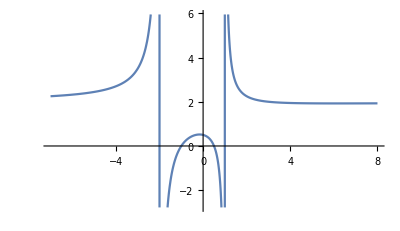

```mathematica
f1[x_]:=Expand[((2x^2)+x-1)/((x^2)+x-2)]
Plot[f1[x],{x,-7,8},AspectRatio->Automatic]
```

```mathematica
(*El dominio son todos los numeros reales excepto -2 y 1.Tiene una asintota horizontal cuando x tiende a infinito y es cuando el limite=2 . Y tiene dos asintotas verticales, una en x=-2 y otra en x=1*)
```

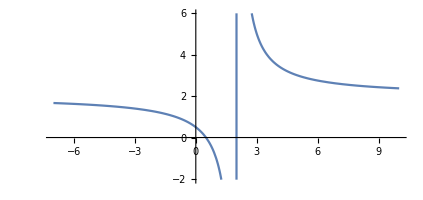

```mathematica
f2[x_]:=Expand[((2x^2)+x-1)/((x^2)-x-2)]
Plot[f2[x],{x,-7,10},AspectRatio->Automatic]
```

```mathematica
(*El dominio son todos los numeros reales excepto 2 y -1.Tiene una asintota horizontal cuando x tiende a infinito y es cuando el limite=2 . Tiene una sola asintota vertical en x=2*)
```

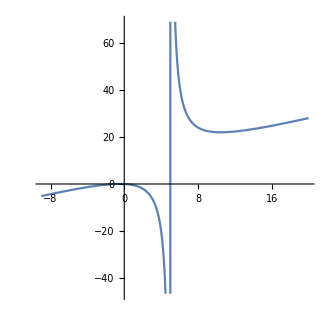

```mathematica
f3[x_]:=Expand[((x^3)-x)/((x^2)-6x+5)]
Plot[f3[x],{x,-9,20},AspectRatio->1]
```

```mathematica
(*El dominio de f3(x) son todos los reales menos x=5 y x=1. No hay asintota horizontal, entonces la hay oblicua. La asintota vertical es en x=5*)
```

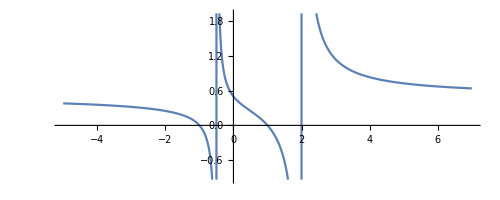

```mathematica
f4[x_]:=Expand[((x^2)-1)/((2x^2)-3x+-2)]
Plot[f4[x],{x,-5,7},AspectRatio->Automatic]
```

```mathematica
(*El dominio son todos los reales menos x=2 y x=-1/2. La asintota horizontal es el limite de la funcion cuando x tiende a +-INF y es en y=1/2. Tiene dos asintotas verticales que son en x=-1/2 y x=2*)
```

```mathematica
f5[x_]:=Expand[(1+(x^4))/((x^2)-(x^4))]
```

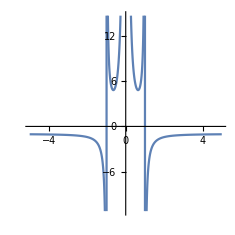

```mathematica
Plot[f5[x],{x,-5,5},AspectRatio->1]
```

```mathematica
(*El dominio de la funcion son todos os reales menos x=1, x=0, x=-1. La asintota horizontal es en y=-1. Hay tres asintotas verticales y son en x=0,x=1,x=-1*)
```

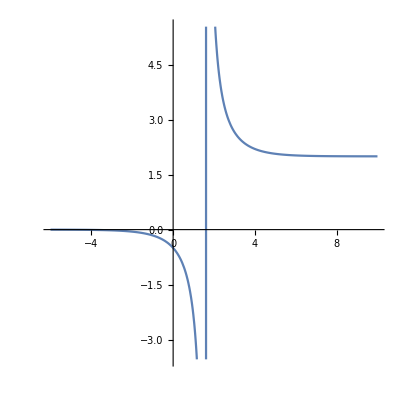

```mathematica
f6[x_]:=Expand[(2(E^x))/((E^x)-5)]
Plot[f6[x],{x,-6,10},AspectRatio->1]
```

```mathematica
(*El dominio son todos los numeros reales menos ln5. Tiene asinto horizontal en y=0 y y=2. Tiene asinto vertical en x=ln5 *)
```

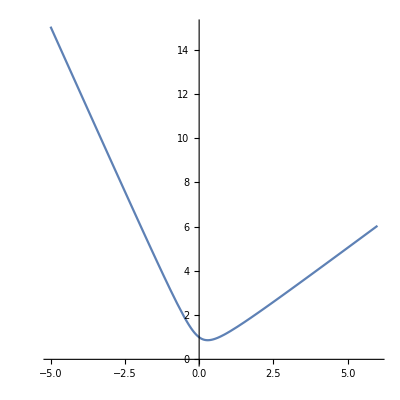

```mathematica
f7[x_]:=Expand[Sqrt[4(x^2)+1]-x]
Plot[f7[x],{x,-5,6},AspectRatio->1]
```

```mathematica
(*Dominio: todos los reales. No tiene asíntotas verticales ni horizontales*)
```

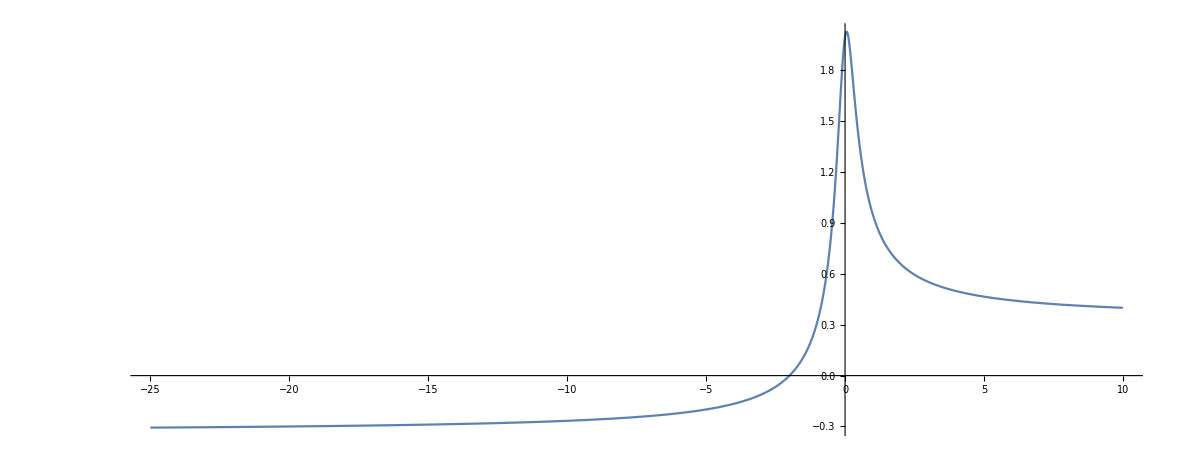

```mathematica
f8[x_]:=Expand[(x+2)/(Sqrt[(9x^2)+1])]
Plot[f8[x],{x,-25,10},AspectRatio->Automatic]
```

```mathematica
(*Dominio: son todos los reales. Las asintotas horizontales es en y=+-1/3. No tiene as[intotas verticales porque el denominador nunca se hace cero*)
```

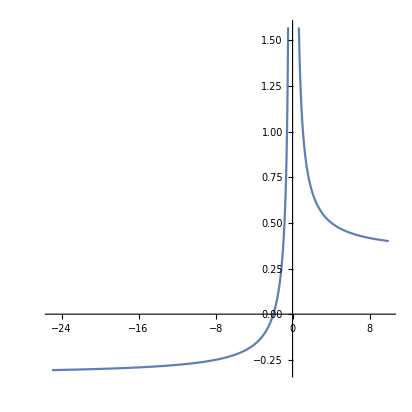

```mathematica
f9[x_]:=Expand[(x+2)/(Sqrt[(9x^2)-1])]
Plot[f9[x],{x,-25,10},AspectRatio->1]
```

```mathematica
(*El dominio es (-INF,-1/3)U(1/3,INF). La asintota horizontal es en y=+-1/3. No tiene asintota vertical*)
```

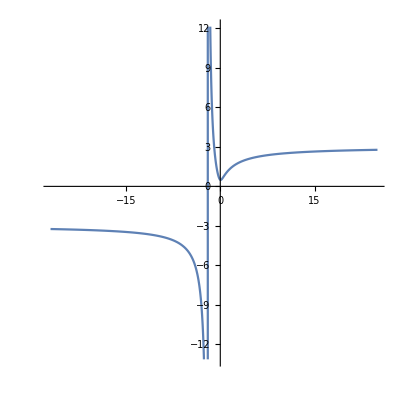

```mathematica
f10[x_]:=Expand[(Sqrt[(9x^2)+1])/(x+2)]
Plot[f10[x],{x,-27,25},AspectRatio->1]
```

```mathematica
(*Dominio, son todos los reales excepto x=-2. Tiene dos asintotas hoizontales, que son en y=-3 y y=3. Tiene una sola asintota vertical en x=-2 *)
```

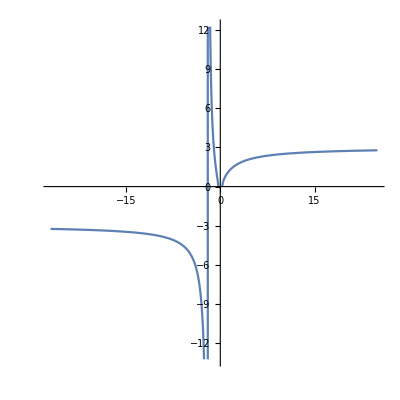

```mathematica
f11[x_]:=Expand[(Sqrt[(9x^2)-1])/(x+2)]
Plot[f11[x],{x,-27,25},AspectRatio->1]
```

```mathematica
(*Dominio: (-INF,-2)U(-2,-1/3]U[1/3,+INF). Tiene dos asintotas hoizontales, que son en y=-3 y y=3. Tiene una sola asintota vertical en x=-2 *)
```

```mathematica
(* d)Las funciones que tienen asintota horizontal son: f0(x), f1(x),f2(x),f4(x),f5(x),f6(x),f8(x),f9(x),f10(x) y f11(x). Esto sucede porque cuando x tiene al infinito la funcion seguira creciendo o decreciendo infinitamente, siempre acercandose mas y mas a un punto pero sin tocarlo nunca *)
(* e)Las funciones que tienen dos asintotas horizontales, son: f6(x),f8(x),f9(x),f10(x) y f11(x), esto sucede en el caso de f8(x),f9(x),f10(x) y f11(x) porque tienen una raiz cuadrada en el denominador lo que genera dos valores para y, iguales en magnitud pero distintos en signo. En el caso de f6, sucede porque es distinto que el exponente x tienda al infinito negativo que al infinito positivo, *)
(* f) f3(x) y f7(x) no tienen asintota horizontal porque la tienen oblicua*)


(* g)Falso, En algunos casos se puede factorizar el numerador y el denominador, así se evita la asíntota y la gráfica puede quedar como una recta*) (*A simple vista pordría parecer que la asíntota es en x=2 pero al factorizar me queda una ecuacion igual a (x+2) sólo que con un hueco en x=2 ya que la funcion no estaria definida en ese punto*)
```

SetDelayed::write: Tag Times in g x_ is Protected. ButtonBox["»",
Appearance->{Automatic, None},
BaseStyle->"Link",
ButtonData:>"paclet:ref/message/General/write",
ButtonNote->"SetDelayed::write"]

```mathematica
(* d) f0(x), f1(x), f2(x), f4(x), f5(x), f6(x), f8(x), f9(x), f10(x), f11(x)  tienen asintota horizontal ya que el limite de cuando x tiende a infinito se acerca cada vez mas a un valor del eje "y" pero sin tocarlo nunca por mas que se acerque *)
(* e) f8(x), f9(x), f10(x), tienen dos asintotas horizontales, esto se debe a que existe una raiz cuadrada, asi que cuando x que esta elevada al cuadrado, tiende al infinito, se generan dos valores de "y"  *)
(* f) f(3) y f7(x) no tienen asintota horizontal porque la tienen oblicua *)
(* g) Es falso porque en algunos casos se pueden factorizar el numerador y el denominador haciendo que la grafica resulte algo sin asintotas, quizas una recta de apariencia normal que no esta definida en uno de sus punto. Un ejemplo seria ((x^2)-4)/(x-2 que factorizando resultaria la grafica de (x+2) sin tocar el punto x=2*)
```

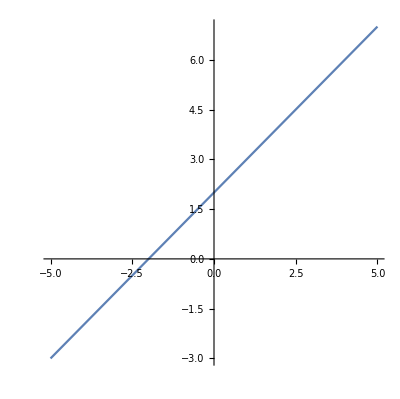

SetDelayed::write: Tag Times in g x_ is Protected.

SetDelayed::write: Tag Times in f15 x_ is Protected.

SetDelayed::write: Tag Times in f20 x_ is Protected.

```mathematica
g[x_]:=Expand[((x^2)-4)/(x-2)]
Plot[g[x],{x,-5,5},AspectRatio->Automatic]
```

```mathematica
(* h)Hay asintota oblicua cuando el limite cuando x tiene de infinito no se ciñe a una recta horizontal sino a una recta con pendiente. Ocurre cuando la funcion es una división entre dos polinomios y el grado del numerador supera en 1 al grado del denominador*)
```

```mathematica
3)
```

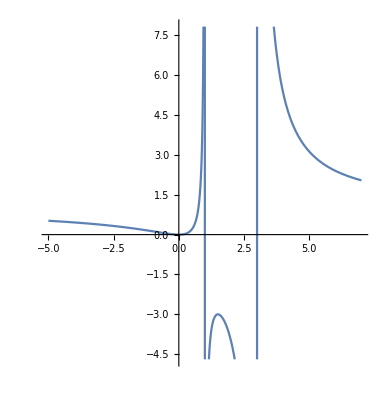

```mathematica
f12[x_]:=Expand[(x^2)/((x^2)-4x+3)]
Plot[f12[x],{x,-5,7},AspectRatio->Automatic]
```

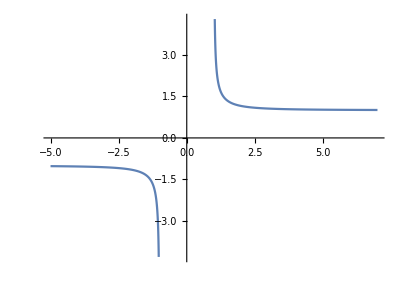

```mathematica
f13[x_]:=Expand[x/Sqrt[(x^2)-1]]
Plot[f13[x],{x,-5,7},AspectRatio->Automatic]
```

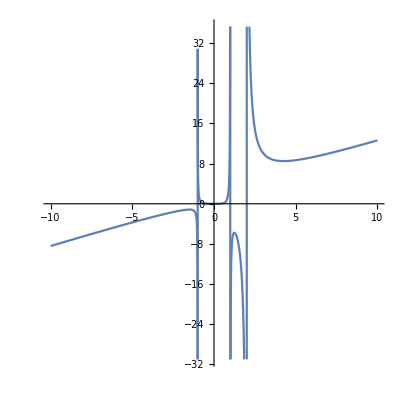

```mathematica
f14[x_]:=Expand[(x^4)/((x-1)(x+1)(x-2))]
Plot[f14[x],{x,-10,10},AspectRatio->1]
```

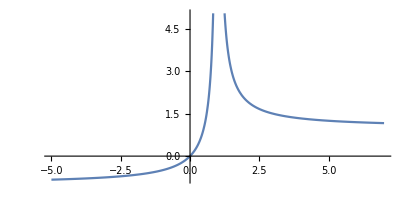

```mathematica
f15[x_]:=Expand[x/(Sqrt[(x-1)^2])]
Plot[f15[x],{x,-5,7},AspectRatio->Automatic]
```